## Dileptons spectrum

### Preface

```mathematica
Needs["PlotLegends`"];
SetDirectory["/home/moosmann/mathematica/montecarlo"]
(*m=105.658369 10^6 ; muon mass*)
```

/home/moosmann/mathematica/montecarlo

Center of mass energy in collision s^(1/2) = 1.96 Tev. Absolute momentum 0 < p_max<s^(1/2)/2.
SU(2)-Yang-Mills scale λ given by λ = y mu, where y parameterizes the uncertainty in the relation between λ and mu. Choose y = 1/2.
Hagedorn temperature T_H is given by T_H= 11.24/(2π) y mu. Assume further T ≈T_H

### Di-fermion spectrum

Di- and Multi- muon vertices are reconstructed for angles θ≤ 36 °, Cos[θ] ≥ cosmin.
Substitute x1 by a function of X, x2 and θ solving the invariant mass relation X^2 = (x1 + (x2))^2 for x2, with X^2=M^2/mu^2≥4 and cos = Cos[θ]:

```mathematica
Block[{solx1m},
{solx1p,solx1m}=Evaluate[x1/.Simplify[Solve[X^2==2(1+Sqrt[1+x1^2]Sqrt[1+x2^2]-x1 x2 cos),x1]]];
solx1p]
```

-(cos (-2+X^2) x2+√((1+x2^2) (-4 X^2+X^4+4 (-1+cos^2) x2^2)))/(-2+2 (-1+cos^2) x2^2)

The denominator  1+Sin[θ]^2 x2^2 is always positive. The term Cos[θ](X^2-2)x2 alike, since X=M/m≥2 and 0≤θ≤π/2.   
The square root needs to be positive (-4 X^2+X^4+4 (-1+cos^2) x2^2)≥0  in order that the solution for x1 is real:

```mathematica
solx1sqrtcon=Boole[(-4 X^2+X^4+4 (-1+cos^2) x2^2)>0];
```

The second solution for x1 is unphysical, since in order to be positive the unequality x2^2≥ X^4/4-X^2 needs to be fullfilled, but the maximum value for x2 allowed by the invariant mass relation (where x1=0) is  X^4/4-X^2.

Moduli space (surface) for the boundary condition of solx1poscon of the squartic term -4 X^2+X^4+4 (-1+cos^2) x2^2 set to 0 :

```mathematica
Block[{Xf=4},TableForm[{{
Labeled[Plot3D[Sqrt[(X^4-4 X^2)/(4-4cos)],{X,2,Xf},{cos,0,.99},AxesLabel->{"X","Cos[θ]","x2"},Filling->Bottom,PlotRange->All,Mesh->False],"Moduli space for the positive solution of x1"],Labeled[Plot3D[Sqrt[1-(X^4-4 X^2)/(4 x2^2)],{X,2,Xf},{x2,0.1,Xf},AxesLabel->{"X","x2","Cos[θ]"},PlotRange->{0,1},Mesh->False],"Moduli space for the positive solution of x1" ]
}}]
]
```

Jacobian jx1X for ⅆx1 = 2 X jx1X ⅆX with X=M/m.Terms inducing higher order differentials in the integral are omitted:

```mathematica
jx1Xp=Simplify[1/D[2(1+Sqrt[1+x1^2]Sqrt[1+x2^2]-x1 x2 cos),x1]/.x1->solx1p];
```

Condition for the emission angle Cos[θ]=n1 · n2 ≥ cosmin, where n1 and n2 are unit vector in the directon of the emitted fermions:

```mathematica
Block[{n},
n[cos_,p_]:={Sqrt[1-cos^2]Cos[2π p],Sqrt[1-cos^2]Sin[2π p],cos};
cos12=n[cos1,p1]. n[cos2,p2];
angcon=Boole[Evaluate[cos12]>cosmin];
]
```

Transversal impuls cut-off for p_(1/,2,transveral)>5GeV:

```mathematica
ptcut=Boole[Sqrt[1-cos1^2]x1> (ptmin  10^9)/(105.658369 10^6)]Boole[Sqrt[1-cos2^2]x2>(ptmin  10^9)/(105.658369 10^6)]/.{x1->solx1p};
```

### Plots

#### Plot function

```mathematica
Remove[mcplot];

mcplot[yy_,CosMin_,acgoal_,prgoal_,partlist_List,Xmax_:10,points_:40,pt_]:=
Block[{dX=(Xmax-2)/points,y=yy,cosmin=CosMin,ptmin=pt,cos=cos12,plot,int,time},

int= Evaluate[
ptcut angcon solx1sqrtcon jx1Xp
 solx1p^3/Sqrt[solx1p^2+1] 1/(Exp[1/(11.24/(2π)y) Sqrt[1+solx1p^2]]+1) 
x2^3/Sqrt[x2^2+1] 1/(Exp[1/(11.24/(2π)y) Sqrt[1+x2^2]]+1)
];

{time,plot}=Timing[ListPlot[
Table[{X,

X (2π)^2NIntegrate[
int,
{x2,0,Sqrt[X^2(X^2-1)/4]},{cos1,-1,1},{cos2,-1,1},{p1,0,1},{p2,0,1},
Method->{"AdaptiveQuasiMonteCarlo","Partitioning"->partlist},
AccuracyGoal->acgoal,
PrecisionGoal->prgoal
]},{X,2,Xmax,dX}

],
AxesLabel->{"√X=M/m","(#  fermions)/(time *surface)"},
PlotRange->Full,
Joined->False,
PerformanceGoal->"Quality",
PlotLabel->Text@TableForm@{{"y =",y,",   cosmin =",cosmin,",   AccuracyGoal =",acgoal,",   PrecisionGoal =",acgoal,",   Partitioning =",ToString[partlist]}},
ImageSize->Scaled[.3]
]];

Export["plot-y"<>ToString[yy]<>"cos"<>ToString[Evaluate[IntegerPart[cosmin]]]<>"Acc"<>ToString[acgoal]<>"Pre"<>ToString[prgoal]<>"Part"<>ToString[partlist[[1]]]<>ToString[partlist[[2]]]<>ToString[partlist[[3]]]<>ToString[partlist[[4]]]<>ToString[partlist[[5]]],plot,"eps"];

TableForm[{time,plot}]

];
```

#### Plots. y=1, cosmin=0

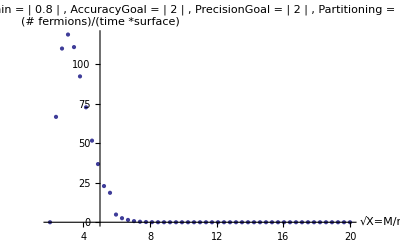
532.013
-Graphics-

```mathematica
mcplot[1,0.8,2,2,{1,1,1,1,1},20,50,0]
```

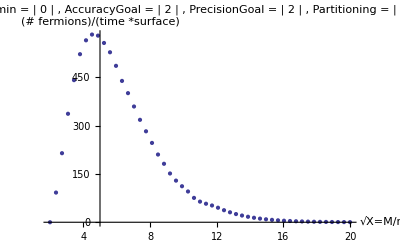
```mathematica
{{431.498967}, {-Graphics-}}
```

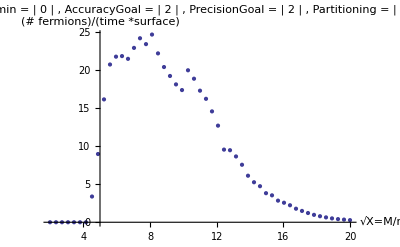
```mathematica
{{80.185011}, {-Graphics-}}
```

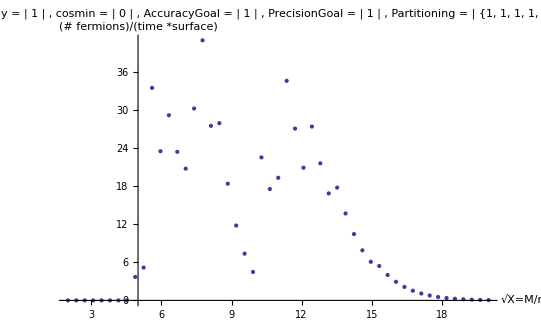
```mathematica
{{4.496281000000003}, {-Graphics-}}
```

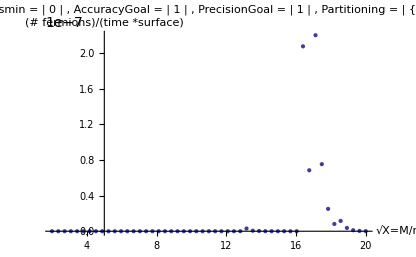
```mathematica
{{4.532282999999996}, {-Graphics-}}
```

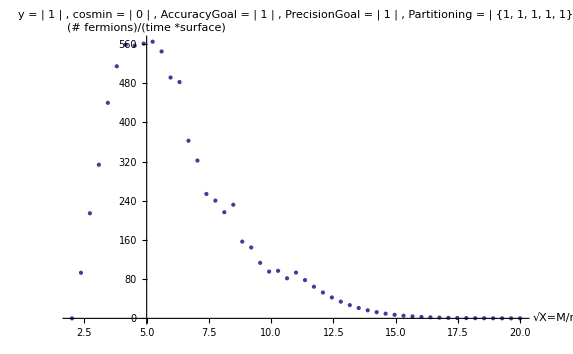
```mathematica
{{11.520719999999997}, {-Graphics-}}
```

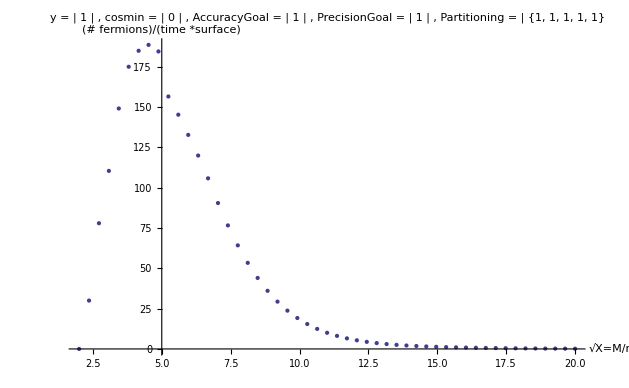
```mathematica
{{5.108320000000007}, {-Graphics-}}
```

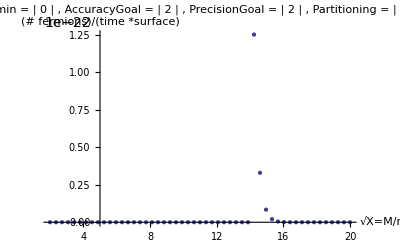
4.54028
-Graphics-

```mathematica
mcplot[1,0,2,2,{1,1,1,1,1},20,50]
```

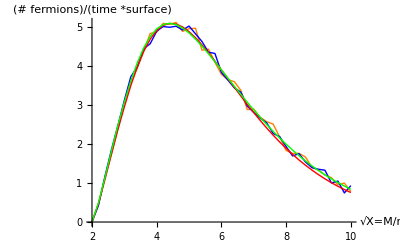
225.09
-Graphics-

```mathematica
mcplot[1,0,1,1,{2,2,2,2,2},10,40]
```

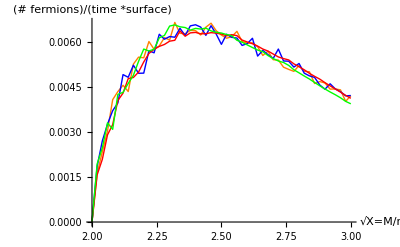

```mathematica
mcplot[1,0,2,2,{2,2,2,2,2}]
```

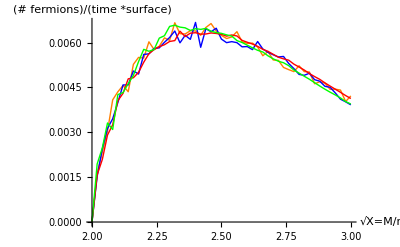

```mathematica
mcplot[1,0,3,3,{2,2,2,2,2}]
```

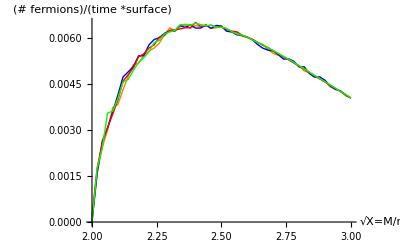

```mathematica
mcplot[1,0,2,2,{3,3,3,3,3}]
```

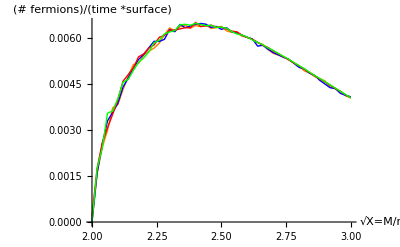

```mathematica
mcplot[1,0,3,3,{3,3,3,3,3}]
```

#### Plots. y = 1, cosmin = .8

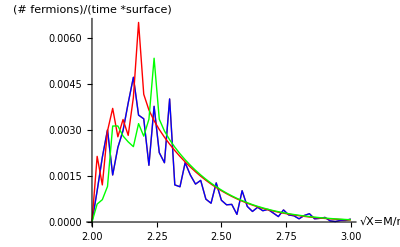

```mathematica
mcplot[1,0.8,1,1,{1,1,1,1,1}]
```

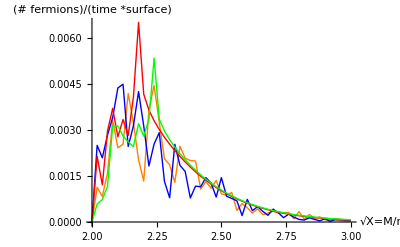

```mathematica
mcplot[1,0.8,2,2,{1,1,1,1,1}]
```

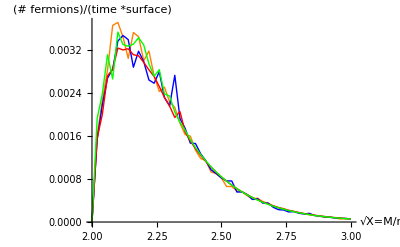

```mathematica
mcplot[1,0.8,1,1,{2,2,2,2,2}]
```

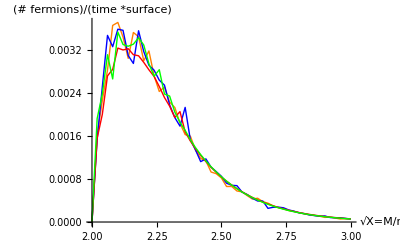

```mathematica
mcplot[1,0.8,2,2,{2,2,2,2,2}]
```

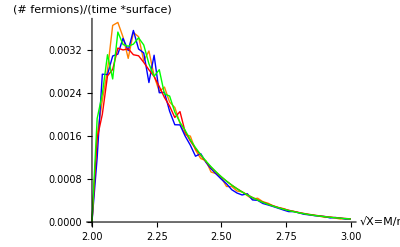

```mathematica
mcplot[1,0.8,3,3,{2,2,2,2,2}]
```

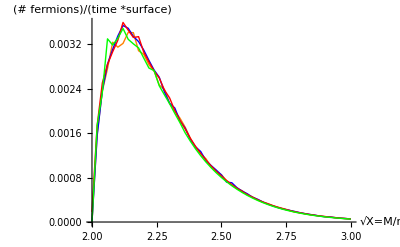

```mathematica
mcplot[1,0.8,2,2,{3,3,3,3,3}]
```

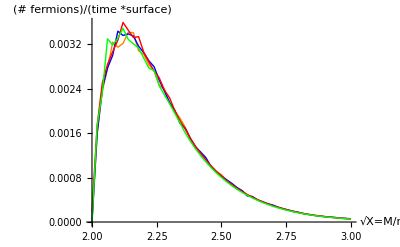

```mathematica
mcplot[1,0.8,3,3,{3,3,3,3,3}]
```

#### Plots. y = 1, cosmin = .6

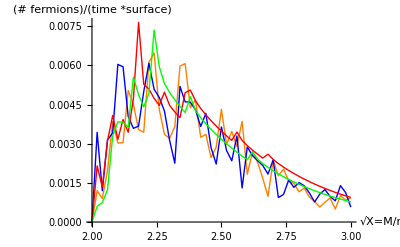

```mathematica
mcplot[1,0.6,1,1,{1,1,1,1,1}]
```

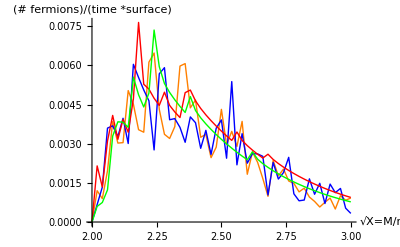

```mathematica
mcplot[1,0.6,2,2,{1,1,1,1,1}]
```

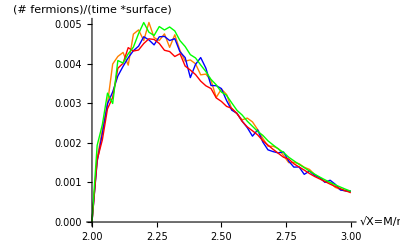

```mathematica
mcplot[1,0.6,1,1,{2,2,2,2,2}]
```

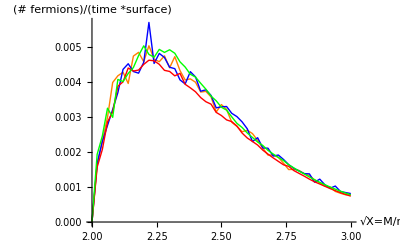

```mathematica
mcplot[1,0.6,2,2,{2,2,2,2,2}]
```

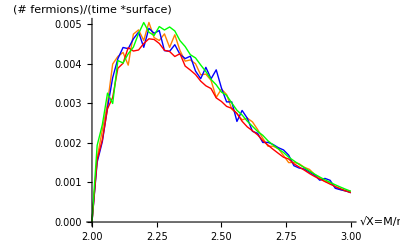

```mathematica
mcplot[1,0.6,3,3,{2,2,2,2,2}]
```

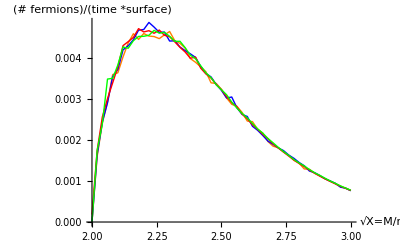

```mathematica
mcplot[1,0.6,2,2,{3,3,3,3,3}]
```

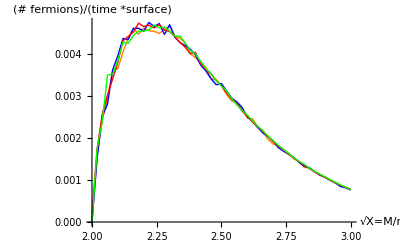

```mathematica
mcplot[1,0.6,3,3,{3,3,3,3,3}]
```

#### Plots. y = 1, cosmin = .4

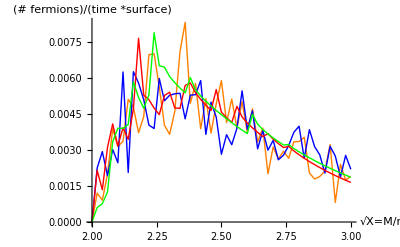

```mathematica
mcplot[1,0.4,1,1,{1,1,1,1,1}]
```

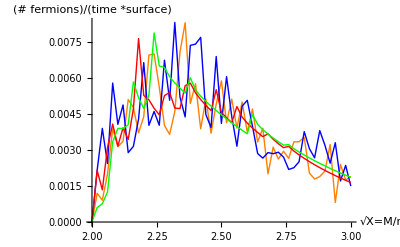

```mathematica
mcplot[1,0.4,2,2,{1,1,1,1,1}]
```

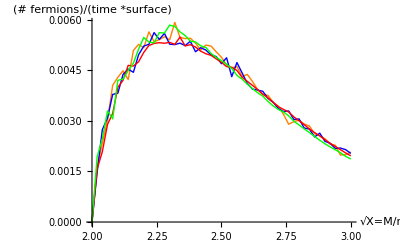

```mathematica
mcplot[1,0.4,1,1,{2,2,2,2,2}]
```

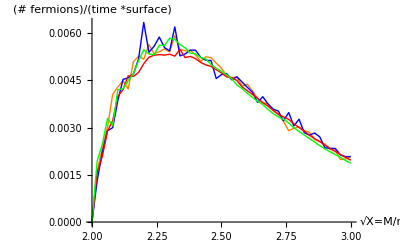

```mathematica
mcplot[1,0.4,2,2,{2,2,2,2,2}]
```

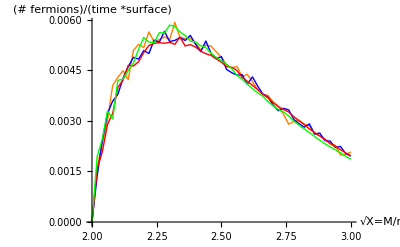

```mathematica
mcplot[1,0.4,3,3,{2,2,2,2,2}]
```

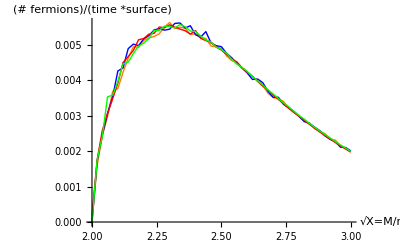

```mathematica
mcplot[1,0.4,2,2,{3,3,3,3,3}]
```

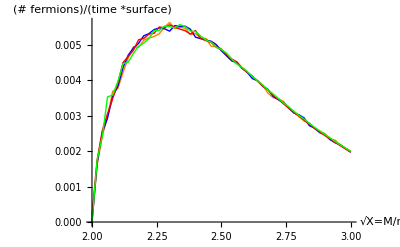

```mathematica
mcplot[1,0.4,3,3,{3,3,3,3,3}]
```

#### Plots. y = 1, cosmin = .2

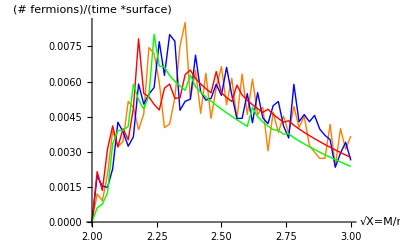

```mathematica
mcplot[1,0.2,1,1,{1,1,1,1,1}]
```

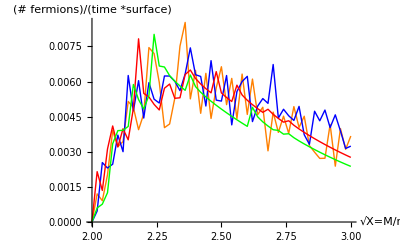

```mathematica
mcplot[1,0.2,2,2,{1,1,1,1,1}]
```

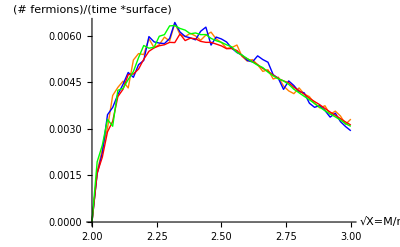

```mathematica
mcplot[1,0.2,1,1,{2,2,2,2,2}]
```

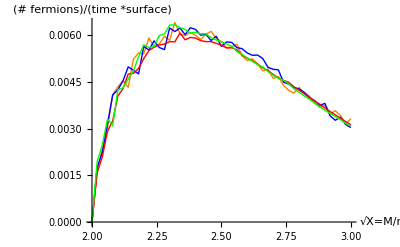

```mathematica
mcplot[1,0.2,2,2,{2,2,2,2,2}]
```

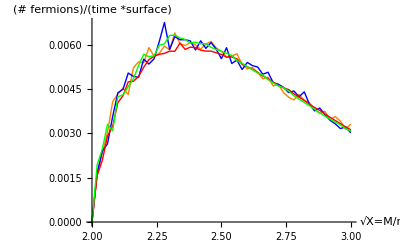

```mathematica
mcplot[1,0.2,3,3,{2,2,2,2,2}]
```

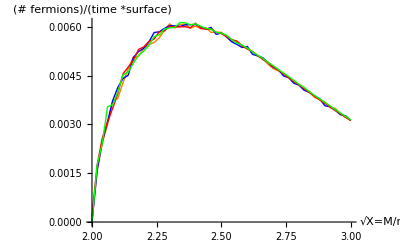

```mathematica
mcplot[1,0.2,2,2,{3,3,3,3,3}]
```

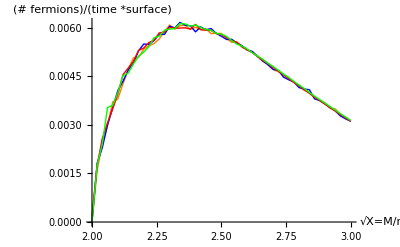

```mathematica
mcplot[1,0.2,3,3,{3,3,3,3,3}]
```

#### Plots. y = 1, cosmin =0

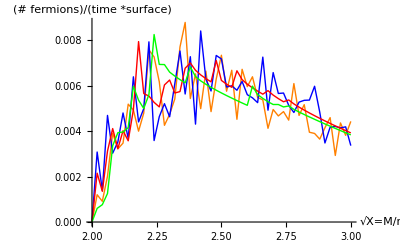

```mathematica
mcplot[1,0,1,1,{1,1,1,1,1}]
```

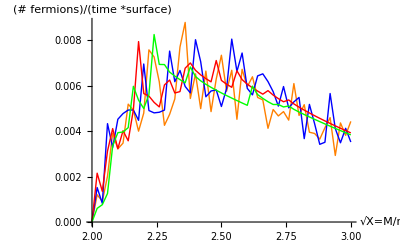

```mathematica
mcplot[1,0,2,2,{1,1,1,1,1}]
```

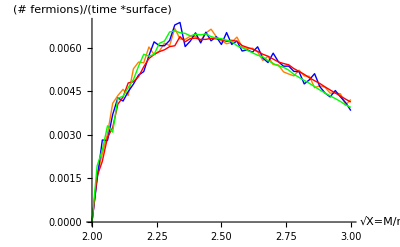

```mathematica
mcplot[1,0,1,1,{2,2,2,2,2}]
```

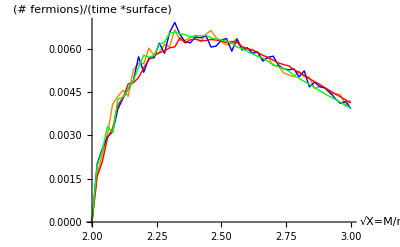

```mathematica
mcplot[1,0,2,2,{2,2,2,2,2}]
```

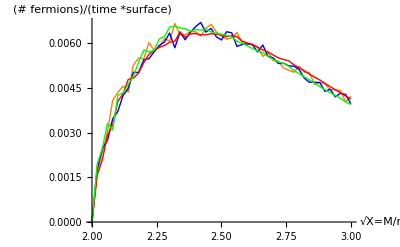

```mathematica
mcplot[1,0,3,3,{2,2,2,2,2}]
```

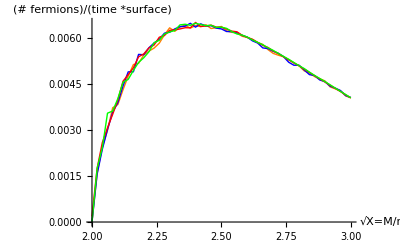

```mathematica
mcplot[1,0,2,2,{3,3,3,3,3}]
```

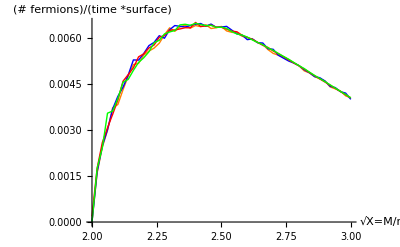

```mathematica
mcplot[1,0,3,3,{3,3,3,3,3}]
```

#### Plots. y = 0.75, cosmin =.8

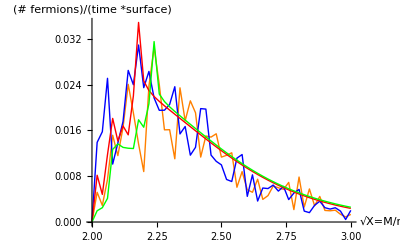

```mathematica
mcplot[0.75,0.8,1,1,{1,1,1,1,1}]
```

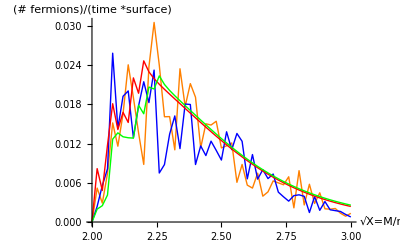

```mathematica
mcplot[0.75,0.8,2,2,{1,1,1,1,1}]
```

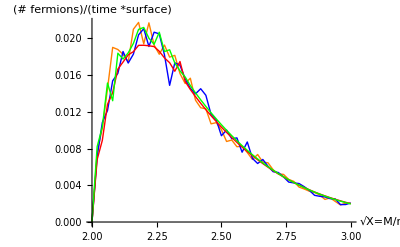

```mathematica
mcplot[0.75,0.8,1,1,{2,2,2,2,2}]
```

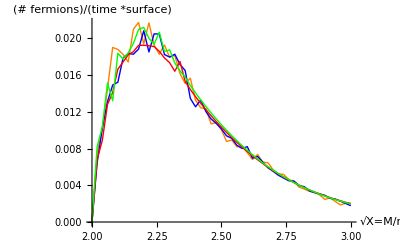

```mathematica
mcplot[0.75,0.8,2,2,{2,2,2,2,2}]
```

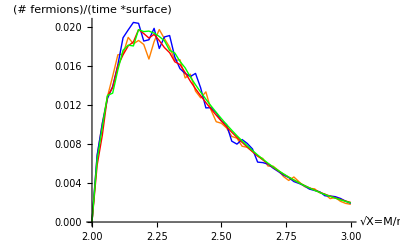

```mathematica
mcplot[0.75,0.8,3,3,{2,2,2,2,2}]
```

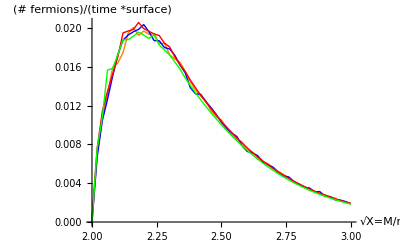

```mathematica
mcplot[0.75,0.8,2,2,{3,3,3,3,3}]
```

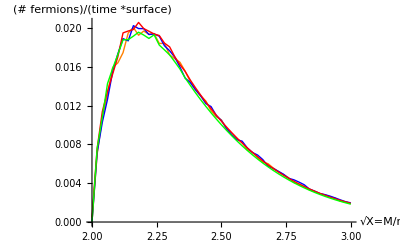

```mathematica
mcplot[0.75,0.8,3,3,{3,3,3,3,3}]
```

#### Plots. y = 0.75, cosmin =.4

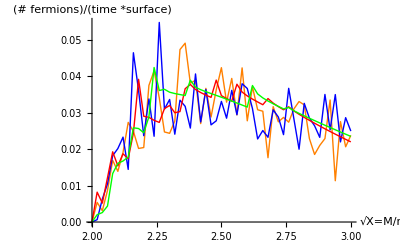

```mathematica
mcplot[0.75,0.4,1,1,{1,1,1,1,1}]
```

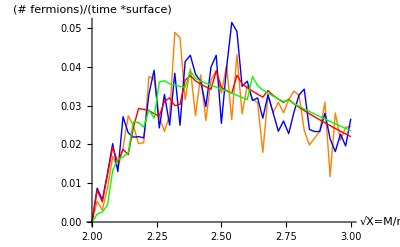

```mathematica
mcplot[0.75,0.4,2,2,{1,1,1,1,1}]
```

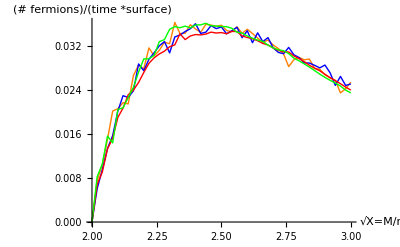

```mathematica
mcplot[0.75,0.4,1,1,{2,2,2,2,2}]
```

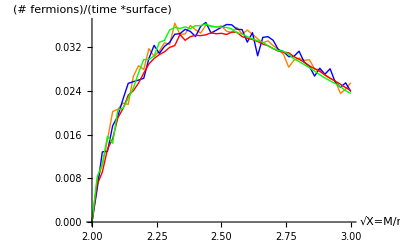

```mathematica
mcplot[0.75,0.4,2,2,{2,2,2,2,2}]
```

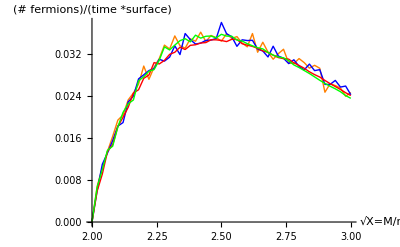

```mathematica
mcplot[0.75,0.4,3,3,{2,2,2,2,2}]
```

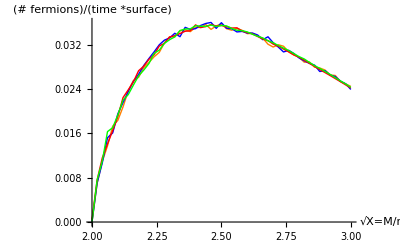

```mathematica
mcplot[0.75,0.4,2,2,{3,3,3,3,3}]
```

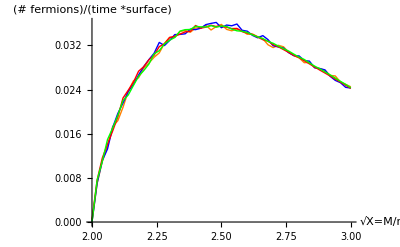

```mathematica
mcplot[0.75,0.4,3,3,{3,3,3,3,3}]
```

#### Plots. y = 0.75, cosmin =0

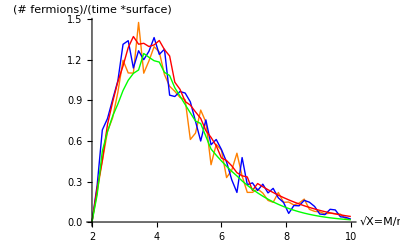
{24.0815,-Graphics-}

```mathematica
Timing@mcplot[0.75,0,1,1,{1,1,1,1,1}]
```

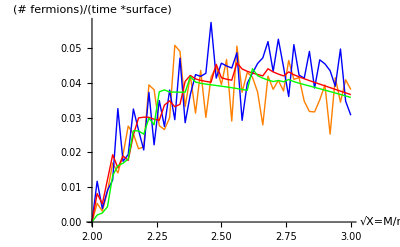

```mathematica
mcplot[0.75,0,2,2,{1,1,1,1,1}]
```

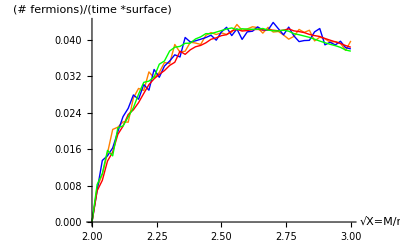

```mathematica
mcplot[0.75,0,1,1,{2,2,2,2,2}]
```

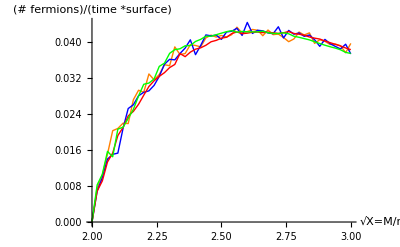

```mathematica
mcplot[0.75,0,2,2,{2,2,2,2,2}]
```

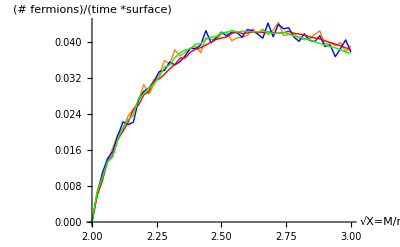

```mathematica
mcplot[0.75,0,3,3,{2,2,2,2,2}]
```

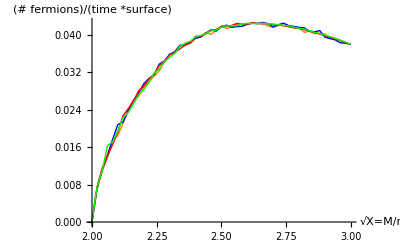

```mathematica
mcplot[0.75,0,2,2,{3,3,3,3,3}]
```

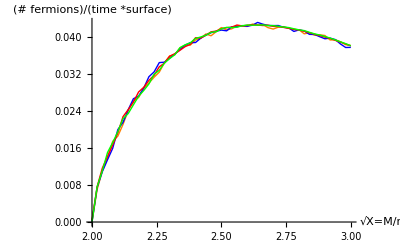

```mathematica
mcplot[0.75,0,3,3,{3,3,3,3,3}]
```

#### Plots y = .5

#### Plots y =.25

### Stuetzstellen

```mathematica
Graphics[
{PointSize[.01],Point[Reap[NIntegrate[f[x]*f[y],{x,0,2},{y,0,2},EvaluationMonitor:>Sow[{x}]]][[2,1]]]},Axes->True,PlotRange->{{-1,1},{-1,1}}]
```

```mathematica
f[x_]:=x^3;
```

```mathematica
mclist=Reap[Print@NIntegrate[f[x]*f[y],{x,0,2},{y,0,2},MaxPoints->50000,EvaluationMonitor:>Sow[{x,y}],Method->"QuasiMonteCarlo"]];Length[mclist[[2,1]]]
```

15.9998

50000

```mathematica
StepMonitor:>Print[x]
```

```mathematica
Block[{a,b},Graphics@{Point[Block[{n=1},{a,b}=Reap[NIntegrate[f[x],{x,0,1},Method->"MonteCarlo",EvaluationMonitor:>{Sow[{n,x}];n=n+1;}]]][[2,1]]]};a]
```

1.25267

```mathematica
{x,x,x}/.x-> RandomReal[]
```

{0.596283,0.596283,0.596283}

```mathematica
8
```

### Single fermion spectrum

Differential (w.r.t to x) probality  density of evaporation of a single lepton with x=p/m, where 0 < x < s^(1/2)/2m:

```mathematica
p[x_]:=m^2/(2 π^2)1/Sqrt[1+x^2] x^3/Exp[11.24/(2π)y Sqrt[1+x^2]]/.{m->1,y->1/2};p[x]
```

(ⅇ^(-0.894451 √(1+x^2)) x^3)/(2 π^2 √(1+x^2))

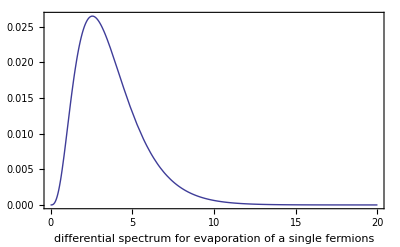

```mathematica
Plot[p[x],{x,0,20},Frame->True,FrameLabel->"differential spectrum for evaporation of a single fermions"]
```

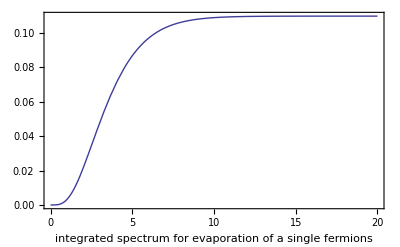

```mathematica
Plot[NIntegrate[p[x],{x,0,xmax}],{xmax,0,20},AxesLabel->{"Probality","x"},Frame->True,FrameLabel->"integrated spectrum for evaporation of a single fermions"]
```

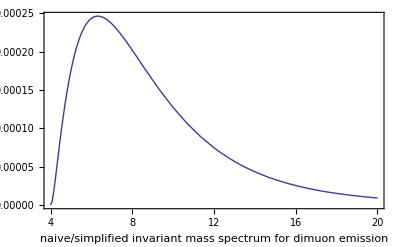

```mathematica
Plot[NIntegrate[solx1poscon*p[x2]p[solx1],{x2,0,20},{cos,0.8,0.99}],{X,4,20},PerformanceGoal->"Speed",Frame->True,FrameLabel->"naive/simplified invariant mass spectrum for dimuon emission"]
```